## Study of the rotational energy of a triaxial rigid rotor

```mathematica
I1=25;
I2=5;
I3=2;
Freq[I_]:=I/I1 Sqrt[(I1-I2)(I1-I3)/(I2*I3)];
En[I_,n_]:=1/(2*I1)I(I+1)+Freq[I](n+1/2);
```

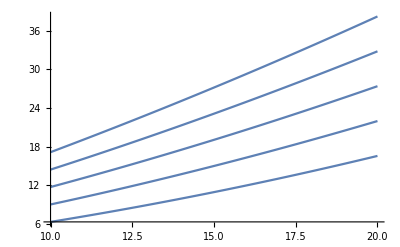

```mathematica
Plot[Table[En[x,k],{k,1,5,1}],{x,10,20}]
```